Your Title Here

```mathematica
r=1;
```

```mathematica
θ=ArcSin[0.2*r/r];
```

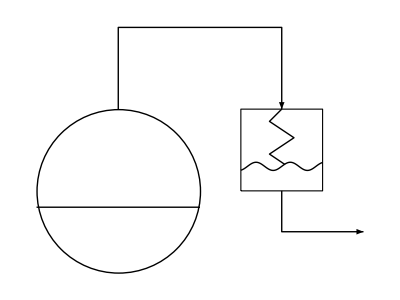

```mathematica
Graphics[{Thick,Arrowheads@0.07,
Sphere[{0,0},r],
Line[{{-r,-0.2*r},{r,-0.2*r}}],
Arrow[{{0,r},{0,2*r},{2*r,2*r},{2*r,r}}],Arrow[{{2*r,0},{2*r,-0.5*r},{3*r,-0.5*r}}],
{EdgeForm@Thick,FaceForm@None,Rectangle[{1.5*r,r},{2.5*r,0}]},
Line[{#+2*r,0.05*Sin[15*#]+0.3}&/@Range[-0.5*r,0.5*r,0.01]],
Line[{{2*r,r},{1.85*r,0.85*r},{2.15*r,0.65*r},{1.85*r,0.45*r},{2.04,0.322}}]
}]
```

```mathematica
Manipulate[
Module[{α,W,T,Psat,Px,Py,p1,p2},
α=2.41;
W={#,Exp[Log[W0]-1/(α-1)*(Log[x0/#]+α*Log[(1-#)/(1-x0)])]}&/@Range[0.01,x0,0.01];

T=325;
Psat[1]=10^(4.72583-1660.652/(T-1.461));
Psat[2]=10^(4.08245-1346.382/(T-53.508));

Px[x_]:=x*Psat[1]+(1-x)*Psat[2];
Py[x_]:=(x/Psat[1]+(1-x)/Psat[2])^-1;

p1=ListPlot[W,Joined->True,PlotStyle->{Thick,Black},PlotRange->{{0.01,x0},{-1,200}},
Frame->True,FrameLabel->{"mole fraction benzene","moles of liquid benzene in still (kmol)"},LabelStyle->{17,Black},ImageSize->{300,400},AspectRatio->Full];

p2=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0,0.6,0]}},
Frame->True,FrameTicks->True,FrameLabel->{"mole fraction benzene","pressure (bar)"},LabelStyle->{17,Black},ImageSize->{300,400},AspectRatio->Full];

Grid@{{p1,p2}}
],
Control[{{x0,0.5,"initial liquid mole frction benzene"},0.1,0.9,0.01,Appearance->"Labeled"}],
Control[{{W0,100,"initial moles of liquid benzene (kmol)"},50,200,1,Appearance->"Labeled"}]
]
```

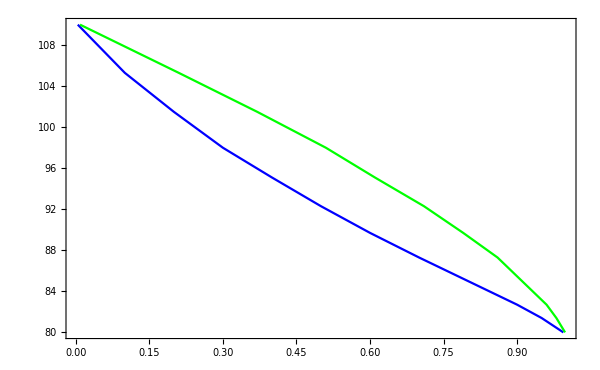





```mathematica
Module[{xB,yB},
xB={{0,110.2},{0.1,105.3},{0.2,101.5},{0.3,98.},{0.4,95.1},{0.5,92.3},{0.6,89.7},{0.700,87.3},{0.8,85.},{0.9,82.7},{0.950,81.4},{1,79.82}};
yB={{0,110.2},{0.21,105.3},{0.37,101.5},{0.51,98.},{0.61,95.1},{0.71,92.3},{0.79,89.7},{0.86,87.3},{0.91,85.},{0.96,82.7},{0.98,81.4},{1,79.82}};

ListPlot[{xB,yB},Joined->True,PlotStyle->{{PointSize@0.02,Blue},{PointSize@0.02,Green}},
PlotRange->{{0,1},{80,110}},Frame->True,ImageSize->600]
]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX